## Load data so we can get tid string

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Options

```mathematica
fName="20180813-orb_4862-densPA_30-Mathematica.csv";
fName="20180813-orb_4862-densPA_45-Mathematica.csv";
fName="20180813-orb_4862-densPA_36-Mathematica.csv";
fName="20180813-orb_4862-densPA_36-MathematicaFINALQQ.csv";
```

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];(*
data=Cases[Import[inDir<>fName,"Table"],{_?NumberQ,___}];
data=Cases[Import[inDir<>fName,"Table"],{_?StringQ,___}]*)
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPots,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
(*{"12:00:29.7","12:00:37.4"},*)
(*{{"12:00:28.5","12:00:37.4"},{"12:00:41.0","12:00:48"}},*)
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
(*{"12:01:22.7","12:01:29.7"}*)
{"09:06:31.288","09:06:51.463"} (*Orbit 4682*)
(*{"12:01:22.7","12:01:29.7"}*) (*BEST?*)
(*{"12:01:20.4","12:01:29.7"}*)
(*{"12:01:17.1","12:01:23.4"}*)];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
{time[[#]]}&/@itvlBounds
```

{{09:06:31.413},{09:06:51.463}}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

```mathematica
tid=tids[[inds1]];
```

## Load other things

```mathematica
newerWifRBgoesto10000=True;
SetDirectory["/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20181120"]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20181120

```mathematica
maxKappaSuff="_maxKappa35";
(*maxKappaSuff="_maxKappa5";*)
```

```mathematica
kFiles=FileNames[RegularExpression["Orb4682_itvl2_kappa-fixT110eV"<>maxKappaSuff<>".*JV(-\\d\\d)?.wdx"]]
```

{Orb4682_itvl2_kappa-fixT110eV_maxKappa35_nRolls6000_JV.wdx}

```mathematica
gFiles=FileNames[RegularExpression["Orb4682_itvl2_Maxwell-fixT96eV.*JV(-\\d\\d)?.wdx"]]
```

{Orb4682_itvl2_Maxwell-fixT96eV_nRolls6000_JV-01.wdx}

RESTORE DATA FILES

```mathematica
For[i=1,i≤ Length@kFiles,i++,
Print[kFiles[[i]]];
If[FileExistsQ[kFiles[[i]]],
Print[Ja];
<<(kFiles[[i]]);
If[i==1,
kMCValsMaster=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
kMCValsMaster = Transpose[(Transpose[kMCValsMaster]~Join~Transpose[kMCVals])];
];
];
]
```

Orb4682_itvl2_kappa-fixT110eV_maxKappa35_nRolls6000_JV.wdx

Ja

```mathematica
For[i=1,i≤ Length@gFiles,i++,
Print[gFiles[[i]]];
If[FileExistsQ[gFiles[[i]]],
Print[Ja];
<<(gFiles[[i]]);
If[i==1,
gMCValsMaster=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
gMCValsMaster = Transpose[(Transpose[gMCValsMaster]~Join~Transpose[gMCVals])];
];
];
]
```

Orb4682_itvl2_Maxwell-fixT96eV_nRolls6000_JV-01.wdx

Ja

```mathematica
kMCValsMaster//Dimensions
```

{4,6000}

```mathematica
gMCValsMaster//Dimensions
```

{4,6000}

```mathematica
gMCValsSub = gMCValsMaster[[;;,1;;6000]];
```

```mathematica
gMCValsSub//Dimensions
```

{4,6000}

```mathematica
nTrialsK=(kMCValsMaster//Dimensions)[[2]];
nTrialsG=(gMCValsSub//Dimensions)[[2]];
```

```mathematica
kMCVals=kMCValsMaster;
gMCVals=gMCValsSub;
Clear[kMCValsMaster,gMCValsMaster,gMCValsSub];
```

## Plots!

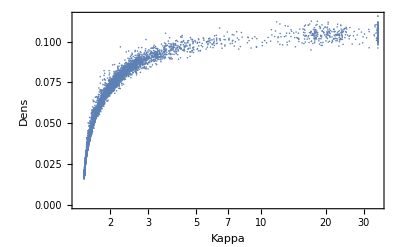

```mathematica
ListLogLinearPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[1,;;]]],2],Frame->True,FrameLabel->{"Kappa","Dens"}]
```

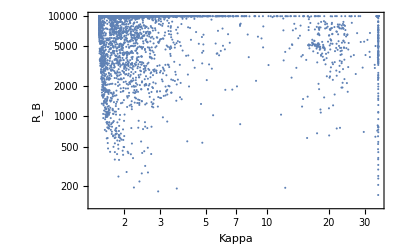

```mathematica
ListLogLogPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[3,;;]]],2],Frame->True,FrameLabel->{"Kappa","R_B"}]
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{100},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:={{2.2,4.2},{0.01,0.11}};
```

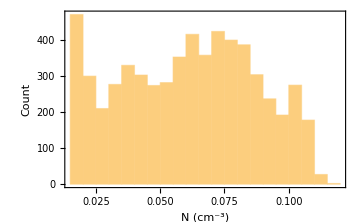
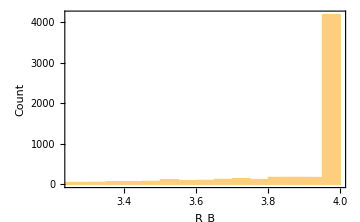
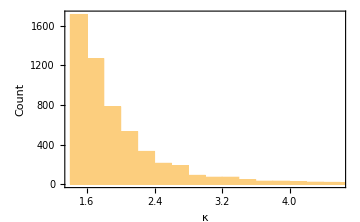
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
Dimensions@kMCVals
```

{4,6000}

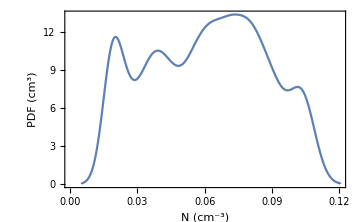
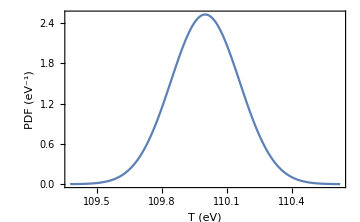
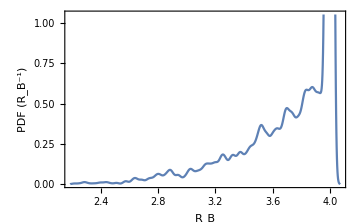
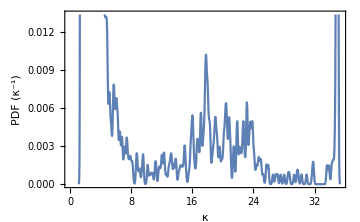

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
n065to085LumpInds=Flatten@Position[kMCVals[[1]],_?(0.065≤ #≤0.085&)];
```

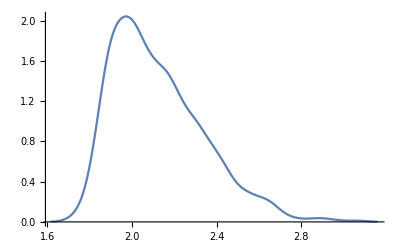

```mathematica
SmoothHistogram[(kMCVals[[4]])[[n065to085LumpInds]]]
```

```mathematica
n0085to01LumpInds=Flatten@Position[kMCVals[[1]],_?(0.085≤ #≤0.1&)];
```

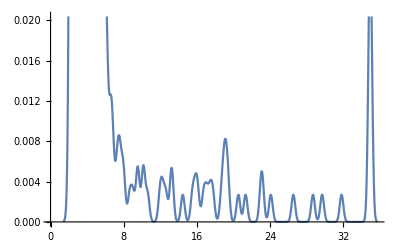

```mathematica
SmoothHistogram[(kMCVals[[4]])[[n0085to01LumpInds]]]
```

```mathematica
n0034to006LumpInds=Flatten@Position[kMCVals[[1]],_?(0.034≤ #≤0.06&)];
```

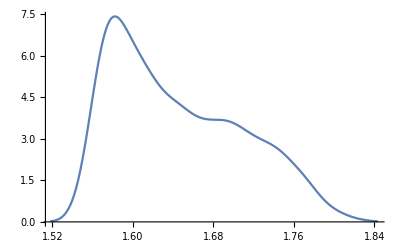

```mathematica
SmoothHistogram[(kMCVals[[4]])[[n0034to006LumpInds]]]
```

## Nye vei, med RE axis

```mathematica
axVals={{3.16,1.54}, {10,2.21} ,{31.6,3.06}, {100,3.69}, {316,4.48}, {1000,6.98}, {3162,14.88}, {10000,39.85}, {20000,76.38}}
```

{{3.16,1.54},{10,2.21},{31.6,3.06},{100,3.69},{316,4.48},{1000,6.98},{3162,14.88},{10000,39.85},{20000,76.38}}

```mathematica
xVals=Round[Log10[axVals[[;;,1]]]*10]/10.//N;
```

```mathematica
log10XwithY=Partition[Riffle[xVals,axVals[[;;,2]]],2];
```

```mathematica
this=Interpolation[log10XwithY]
```

InterpolatingFunction[…]

```mathematica
RBVals={2.5,2.7,3.0,3.5,4.0};
```

```mathematica
REVals=this[RBVals]
```

{4.48,5.06816,6.98,14.88,39.85}

```mathematica
REValsRound=Round[REVals*10]/10.
```

{4.5,5.1,7.,14.9,39.8}

```mathematica
tics=Line[{{#,0.03+0.001},{#,0.03-0.001}}&/@RBVals]
```

Line[{{{2.5,0.031},{2.5,0.029}},{{2.7,0.031},{2.7,0.029}},{{3.,0.031},{3.,0.029}},{{3.5,0.031},{3.5,0.029}},{{4.,0.031},{4.,0.029}}}]

```mathematica
text=Text[#[[2]],{#[[1]],0.35}]&/@Partition[Riffle[RBVals,REValsRound],2]
```

{Text[4.5,{2.5,0.35}],Text[5.1,{2.7,0.35}],Text[7.,{3.,0.35}],Text[14.9,{3.5,0.35}],Text[39.8,{4.,0.35}]}

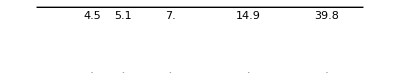

```mathematica
axis=Graphics[{Line[{{2.145,0.4},{4.233,0.4}}],tics,text}]
```

### Etter 20180928, med legend

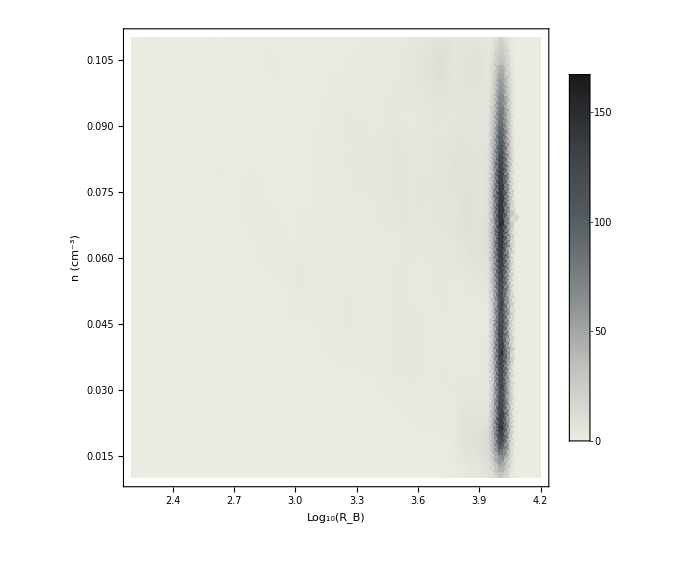

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10(R_B)",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotLegends->Automatic,LabelStyle->Directive[FontSize->22]]
```

```mathematica
BarLegend[{(ColorData[{"GrayTones","Reverse"}][#]&),{0,1}},LabelStyle->Directive[FontSize->22],LegendMarkerSize->{19, 500}]
```

```mathematica
(ColorData[{"GrayTones","Reverse"}][#]&)[0]
```

RGBColor[0.917794, 0.920966, 0.881936]

### Original, før 20180928

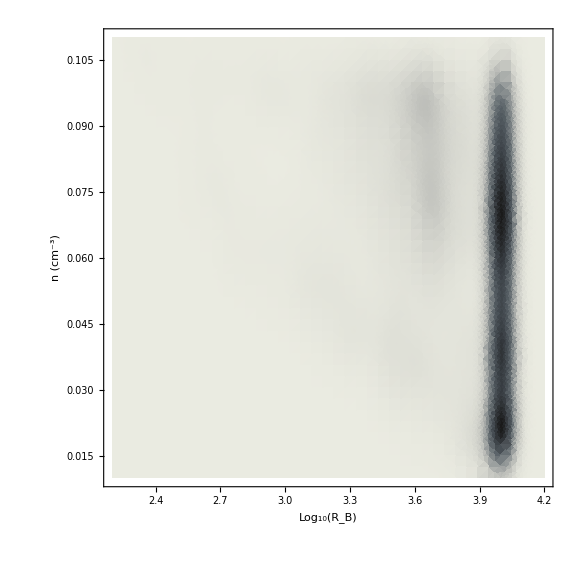

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10(R_B)",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

Maxwellian plots

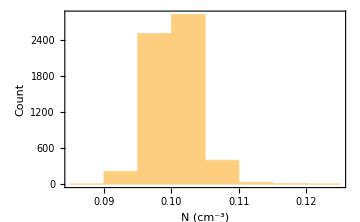
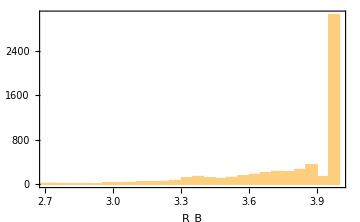
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

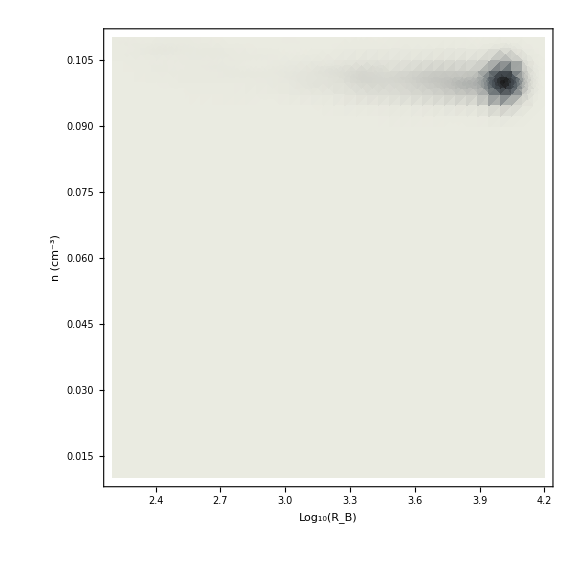

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10(R_B)",Style[ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```